## Angles (the Euler angles)

```mathematica
theta=π/3;
psi=π/4;
phi=π/4;
```

```mathematica
spin=1;
```

## Components of the wave functions

```mathematica
wfc[spin_]:=Table[Table[{spin,M,K},{M,-spin,spin}],{K,-spin,spin}];
```

```mathematica
Print[Length[wfc[spin]]]
```

3

```mathematica
wfc[spin][[1]]
```

{{1,-1,-1},{1,0,-1},{1,1,-1}}

```mathematica
wfc[spin][[2]]
```

{{1,-1,0},{1,0,0},{1,1,0}}

```mathematica
wfc[spin][[3]]
```

{{1,-1,1},{1,0,1},{1,1,1}}

```mathematica
wd=Table[WignerD[wfc[spin][[1,i]],phi,theta,psi],{i,1,Length[wfc[spin][[1]]]}];
wd
```

{-(3 ⅈ)/4,1/2 √(3/2) ⅇ^(-(ⅈ π)/4),1/4}

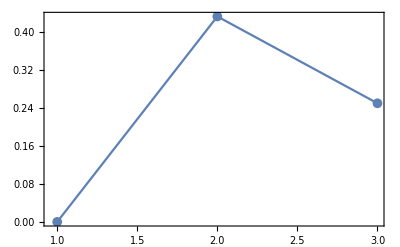

```mathematica
wd=Re[wd];
ListPlot[wd,PlotRange->All,Frame->True,Joined->True,PlotMarkers->{Automatic, Medium}]
```